# Attempt number 2 of problem set 1.1

## Function definition

```mathematica
dxdt[x_, r_] := ( 1/5 + 7/10 * 1/(1 + Exp[80 (1 - x)]) - r*x^4)
d2xdt2[x_, r_] := N[D[dxdt[ξ, r], ξ] /. ξ -> x]
```

## Plot up function to study dynamics

```mathematica
Manipulate[
Show[
Plot[dxdt[x,r],{x,-1,2}],ListPlot[({x,0}/. NSolve[dxdt[x,r]==0,x,Reals]),PlotStyle->Red]
],{r,-10,10}]

Manipulate[Show[
Plot[{ 1/5 + 7/10 * 1/(1 + Exp[80(1-x)]),r*x^4},{x,-1,2}],ListPlot[{x,r*x^4}/.NSolve[1/5 + 7/10 * 1/(1 + Exp[80(1-x)])==r*x^4,x,Reals],PlotStyle->Red]],{r,-10,10}]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

ReplaceAll::reps: {NSolve[dxdt[x,-10]==0,x,]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

ReplaceAll::reps: {NSolve[dxdt[x,-10.]==0,x,]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

General::stop: Further output of NSolve::nsmet will be suppressed during this calculation.

ReplaceAll::reps: {NSolve[dxdt[x,-10.]==0.,x,]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListPlot::lpn: {x,0}/.NSolve[dxdt[x,-10.]==0,x,] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[{x,0}/.NSolve[dxdt[x,-10]==0,x,],PlotStyle→color]].

## Solve fixed points

```mathematica
rValues=Table[r,{r,0.01,1.25, 0.001}];
fixedPoints = Flatten[
   Table[{r, x} /. NSolve[dxdt[x, r] == 0, x, Reals], {r, rValues}], 1
];
fixedPointsWithDerivative = Flatten[
  Table[
    Module[{solutions, derivatives},
      (* Solve for x such that dxdt[x, r] == 0 *)
      solutions = x /. NSolve[dxdt[x, r] == 0, x, Reals];
      
      (* Evaluate the derivative at each solution *)
      derivatives = d2xdt2[#, r] & /@ solutions;
      
      (* Pair each solution with its derivative *)
      Transpose[{ConstantArray[r, Length[solutions]], solutions, derivatives}]
    ],
    {r, rValues}
  ],
  1
]
```

## Plot the fixed points

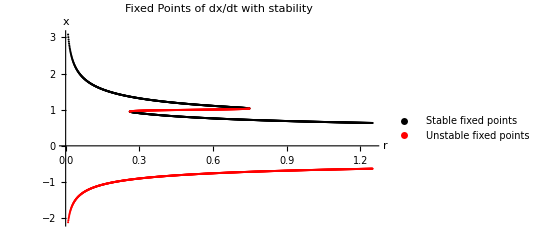

```mathematica
(*Unstable points*)
positiveDerivativePoints = Select[fixedPointsWithDerivative, #[[3]] > 0 &]; 
(*Stable points*)
negativeDerivativePoints = Select[fixedPointsWithDerivative, #[[3]] < 0 &];


ListPlot[
  {negativeDerivativePoints[[All, {1, 2}]], positiveDerivativePoints[[All, {1, 2}]]},
  PlotStyle -> {Directive[Black], Directive[Red]},
  AxesLabel -> {"r", "x"},
  PlotRange -> All,
  PlotLegends -> {"Stable fixed points", "Unstable fixed points"},
  PlotLabel -> "Fixed Points of dx/dt with stability"
]
```

## Determine critical r and it’s x*

```mathematica
eqn1=dxdt[x,r]==0;
eqn2=d2xdt2[x,r]==0;

(*initial guesses from plot*)
x0=0.91;
r0=0.25;

solution=FindRoot[{eqn1,eqn2},{x,x0},{r,r0}];
{criticalX1,criticalR1}={x,r}/. solution;
Print["1: Critical x value: ",criticalX1]
Print["1: Critical r value: ",criticalR1]

x0=1.02;
r0=0.74;

solution=FindRoot[{eqn1,eqn2},{x,x0},{r,r0}];
{criticalX2,criticalR2}={x,r}/. solution;

Print["2: Critical x value: ",criticalX2]
Print["2: Critical r value: ",criticalR2]
```

1: Critical x value: 0.948649

1: Critical r value: 0.260928

2: Critical x value: 1.03372

2: Critical r value: 0.749498

## Retrieve arrays of values

```mathematica
groupedData = GatherBy[fixedPoints, First];

array1 = {};
array2 = {};
array3 = {};
array4 = {};

Do[
  rGroup = groupedData[[i]];
  rValue = rGroup[[1, 1]];
  xs = rGroup[[All, 2]];
  n = Length[xs];

  If[n >= 1,
    AppendTo[array1, {rValue, xs[[1]]}];
  ];

  If[rValue > criticalR1,
    If[n >= 2, AppendTo[array2, {rValue, xs[[2]]}]];
    If[n >= 3 && rValue <= criticalR2,
      AppendTo[array3, {rValue, xs[[3]]}];
    ];
    If[n == 4,
      AppendTo[array4, {rValue, xs[[4]]}];
    ];
  ,
    If[n >= 2, AppendTo[array4, {rValue, xs[[2]]}]];
  ];
, {i, Length[groupedData]}];

array1;
array2;
array3;
array4;
```

## Plot the final plot

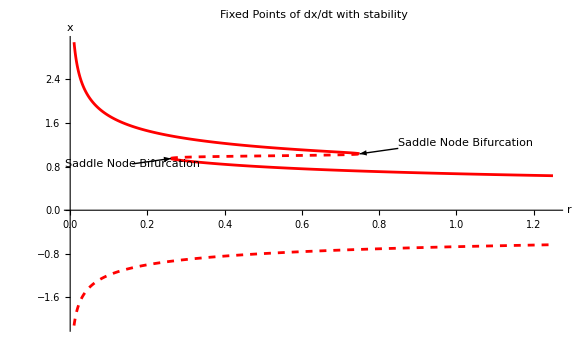

```mathematica
bifur1 = {criticalR1, criticalX1};
bifur2 = {criticalR2, criticalX2};

arrowStart1 = bifur1 + {-0.1, -0.1} ; 
arrowStart2 = bifur2 + {0.1, 0.1}; 

label1 = "Saddle Node Bifurcation"; 
label2 = "Saddle Node Bifurcation"; 



plotLines = ListLinePlot[
  {array1, array2, array3, array4},
  PlotStyle -> {Directive[Dashed, Red], Directive[Red], Directive[Dashed, Red], Directive[Red]}
  ];

Show[plotLines, Epilog -> {
	    {Black, Arrow[{arrowStart1, bifur1}]},
	    Text[label1, arrowStart1, {0, 2}],
	    {Black, Arrow[{arrowStart2, bifur2}]},
	    Text[label2, arrowStart2, {-1, -1}]
	    },
	  AxesLabel -> {"r", "x"},
	  PlotRange -> All,
	  PlotLegends -> {"Stable fixed points", "Unstable fixed points"},
	  PlotLabel -> "Fixed Points of dx/dt with stability"
]
```